```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
SetOptions[Notebooks["elections.nb"][[1]],AutoGeneratedPackage->Automatic]
```

# Recomputing the 2016 election

## Loading the Data

Let’s get the functions from `apportionment.nb`

```mathematica
CloudGet["https://www.wolframcloud.com/objects/e38bf09f-1de6-41d3-864c-eaaf7e320513"];
```

Election results are culled from fec.gov in `getElectionResultsPresidential.nb`  and `getElectionResultsCongress.nb`

```mathematica
electionDataPresident = CloudGet["https://www.wolframcloud.com/objects/085af547-95c3-4daa-9c88-aa7bc343100f"];
electionDataCongress = CloudGet["https://www.wolframcloud.com/objects/ece1bd42-6504-4add-b62a-f70989f29f3f"];
```

```mathematica
electionDataPresident["ME"]
```

<|name→Maine,abbr→ME,entity→Maine, United States,ev_total→4,ev_trump→1.,ev_clinton→3.,votes_trump→335593.,votes_clinton→357735.,votes_others→54599.,votes_total→747927.,winner→<|name→Hillary Clinton,party→D|>|>

As it stands, all states and Washington, D.C. award their electoral votes in a winner-take-all fashion, with two exceptions: Nebraska and Maine split the electoral votes corresponding to their members of the House -- three and two electors, respectively -- according to the winner of each Congressional district. As you see above, in 2016 Donald Trump won one electoral vote in Maine while Clinton carried the other three. There was no division in Nebraska.

Let’s make a function that allocates EVs according to the state election results, leaving the number of electoral votes parameterized since we’re fussing with allocation algorithms. In keeping with 2016 results, we’ll start by giving Trump 25 percent of Maine’s electoral votes, rounded down.

```mathematica
RerunElectionPresidentState[stateAbbr_, stateEVs_:-1] := (
	results = electionDataPresident[stateAbbr];
	EVs = If[stateEVs == -1, statesByAbbreviation[stateAbbr]["evs"]["2010"], stateEVs];
	partial = If[stateAbbr == "ME", Floor[EVs / 4.0], 0];
	EVs = EVs - partial;		
	Dem = If[results["votes_trump"] > results["votes_clinton"], partial, EVs];
	Rep = If[results["votes_trump"] < results["votes_clinton"], partial, EVs];
	<| "abbr" -> stateAbbr, "state" -> statesByAbbreviation[stateAbbr]["name"], "entity" -> statesByAbbreviation[stateAbbr]["entity"], "evs" -> EVs + partial, "R" -> Rep, "D" -> Dem |>
)
```

```mathematica
RerunElectionPresidentState["ME"]
```

<|abbr→ME,state→Maine,entity→Maine, United States,evs→4,R→1,D→3|>

Okay, let’s run an election, starting with a rerun of 2016

```mathematica
RerunElectionPresident[allocation_:houseOfRepresentatives, evsDC_:3] := (
	evs = KeySort@Append[allocation + 2, "DC" -> evsDC];
	states = RerunElectionPresidentState[#, evs[#]]& /@ Keys@evs;
	totalD = Total[#["D"]& /@ states];
	totalR = Total[#["R"]& /@ states];
	<| "result" -> <| "R" -> totalR, "D" -> totalD, "Total" -> (totalD + totalR) |>, "states" -> AssociationThread[Keys@evs, states] |>	
)
```

```mathematica
rerun = RerunElectionPresident[];
rerun["result"]
```

<|R→306,D→232,Total→538|>

This tracks with reality exactly after accounting for “faithless electors,” who cast rogue ballots in the Electoral College.

["https://en.wikipedia.org/wiki/United_States_presidential_election,_2016#cite_note-pledged-2"](https://en.wikipedia.org/wiki/United_States_presidential_election,_2016#cite_note-pledged-2)

```mathematica
{ blue, red, green } = { RGBColor["#00B2FF"], RGBColor["#F15C53"], RGBColor["#01CF0E"] }
```

{RGBColor[0., 0.6980392156862745, 1.],RGBColor[0.9450980392156862, 0.3607843137254902, 0.3254901960784314],RGBColor[0.00392156862745098, 0.8117647058823529, 0.054901960784313725]}

```mathematica
ChartPresidentialElection[electionResults_, perRow_:27] := (
	evsR = #["R"]& /@ electionResults["states"];
	evsD = #["D"]& /@ electionResults["states"];
	evsTotal = #["evs"]& /@ electionResults["states"];
	max = Max[Max@evsR, Max@evsD];
	stateNames = Keys@electionResults["states"];

	colorScales = <| 	
		"state" -> Function[ev, White],	
		"D" -> Function[ev, Blend[Transpose[{{0, max}, { White, blue }}], ev]],
		"R" -> Function[ev, Blend[Transpose[{{0, max}, { White, red }}], ev]],
		"total" -> Function[ev, Blend[Transpose[{{0, max}, { White, green }}], ev]]
	|>;

	(* convert the seating data to items for grid, adding header and footer *)	
	dataAssociations = { AssociationThread[stateAbbrs, stateAbbrs], evsD, evsR, evsTotal };

	itemWidth = 2;
	itemHeight = 1;
	fontSize = 10;

	(* convert each cell to an Item for easier formatting *)
	itemizeCell[{ dataAssociation_, colorScale_ }] := Item[Style[dataAssociation[#], FontSize->fontSize, TextAlignment->Center],
		Background->colorScale[dataAssociation[#]],
		ItemSize->{ itemWidth, itemHeight },
		Alignment -> Bottom]& /@ stateAbbrs;
	
	itemizedRows = Map[
		itemizeCell,
		Transpose[{ dataAssociations, Values@colorScales }]
	];

	totals = { 
		Item[Style["Total", FontSize->fontSize, TextAlignment->Center], Background->White, ItemSize->{ itemWidth * 3, itemHeight }, Alignment -> Bottom],
		Item[Style[Total@evsD, FontSize->fontSize, TextAlignment->Center], Background->colorScales["D"][Total@evsD], ItemSize->{ itemWidth * 3, itemHeight }, Alignment -> Bottom],
		Item[Style[Total@evsR, FontSize->fontSize, TextAlignment->Center], Background->colorScales["R"][Total@evsR], ItemSize->{ itemWidth * 3, itemHeight }, Alignment -> Bottom],
		Item[Style[Total@evsTotal, FontSize->fontSize, TextAlignment->Center], Background->colorScales["total"][Total@evsTotal], ItemSize->{ itemWidth * 3, itemHeight }, Alignment -> Bottom]
	};

	rows = Append[itemizedRows[[#]], totals[[#]]]& /@ Range[4];
	rows[[1]] = Style[#, Bold]& /@ rows[[1]];
	
	parts = First@Partition[rows, { 4, UpTo@perRow }];

	headers = {
		Item[Style["State", FontSize->fontSize, TextAlignment->Right, Bold], ItemSize->{itemWidth * 2, itemHeight}],
		Item[Style["Clinton", FontSize->fontSize, TextAlignment->Right], ItemSize->{itemWidth * 2, itemHeight}],
		Item[Style["Trump", FontSize->fontSize, TextAlignment->Right], ItemSize->{itemWidth * 2, itemHeight}],
		Item[Style["Total", FontSize->fontSize, TextAlignment->Right], ItemSize->{itemWidth * 2, itemHeight}]
	};

	headerRows = Map[Flatten, Transpose[{ headers, # }]& /@ parts, {2}];
	Column[Grid[#, Frame -> All, ItemSize->All, Spacings->{0.2, 0.8}]& /@ headerRows, Spacings -> 0.1]
)
```

```mathematica
ChartPresidentialElection[rerun, 27]
```

State | AK | AL | AR | AZ | CA | CO | CT | DC | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
Clinton | 0 | 0 | 0 | 0 | 55 | 9 | 7 | 3 | 3 | 0 | 0 | 4 | 0 | 0 | 20 | 0 | 0 | 0 | 0 | 11 | 10 | 3 | 0 | 10 | 0 | 0 | 0
Trump | 3 | 9 | 6 | 11 | 0 | 0 | 0 | 0 | 0 | 29 | 16 | 0 | 6 | 4 | 0 | 11 | 6 | 8 | 8 | 0 | 0 | 1 | 16 | 0 | 10 | 6 | 3
Total | 3 | 9 | 6 | 11 | 55 | 9 | 7 | 3 | 3 | 29 | 16 | 4 | 6 | 4 | 20 | 11 | 6 | 8 | 8 | 11 | 10 | 4 | 16 | 10 | 10 | 6 | 3
State | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
Clinton | 0 | 0 | 0 | 4 | 14 | 5 | 6 | 29 | 0 | 0 | 7 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 13 | 3 | 12 | 0 | 0 | 0 | 232
Trump | 15 | 3 | 5 | 0 | 0 | 0 | 0 | 0 | 18 | 7 | 0 | 20 | 0 | 9 | 3 | 11 | 38 | 6 | 0 | 0 | 0 | 10 | 5 | 3 | 306
Total | 15 | 3 | 5 | 4 | 14 | 5 | 6 | 29 | 18 | 7 | 7 | 20 | 4 | 9 | 3 | 11 | 38 | 6 | 13 | 3 | 12 | 10 | 5 | 3 | 538

Let’s see what happens with one of those alternate apportionment algorithms

```mathematica
factorInElectors = CalculateAllocations[435, 3, -2];
adjustedResults = RerunElectionPresident[factorInElectors, 3];
ChartPresidentialElection[adjustedResults]
```

State | AK | AL | AR | AZ | CA | CO | CT | DC | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
Clinton | 0 | 0 | 0 | 0 | 61 | 8 | 6 | 3 | 4 | 0 | 0 | 4 | 0 | 0 | 21 | 0 | 0 | 0 | 0 | 11 | 10 | 3 | 0 | 9 | 0 | 0 | 0
Trump | 3 | 8 | 5 | 11 | 0 | 0 | 0 | 0 | 0 | 31 | 16 | 0 | 5 | 4 | 0 | 11 | 5 | 7 | 7 | 0 | 0 | 1 | 16 | 0 | 10 | 5 | 4
Total | 3 | 8 | 5 | 11 | 61 | 8 | 6 | 3 | 4 | 31 | 16 | 4 | 5 | 4 | 21 | 11 | 5 | 7 | 7 | 11 | 10 | 4 | 16 | 9 | 10 | 5 | 4
State | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
Clinton | 0 | 0 | 0 | 4 | 15 | 4 | 4 | 32 | 0 | 0 | 6 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 13 | 3 | 11 | 0 | 0 | 0 | 236
Trump | 16 | 3 | 4 | 0 | 0 | 0 | 0 | 0 | 19 | 6 | 0 | 21 | 0 | 8 | 3 | 10 | 42 | 5 | 0 | 0 | 0 | 9 | 4 | 3 | 302
Total | 16 | 3 | 4 | 4 | 15 | 4 | 4 | 32 | 19 | 6 | 6 | 21 | 4 | 8 | 3 | 10 | 42 | 5 | 13 | 3 | 11 | 9 | 4 | 3 | 538

As we see, that method does very little to change anything.

## Mapping the Presidential results

```mathematica
imageTrump = ImageCrop[Entity["Person","DonaldTrump::6vv3q"]["Image"], { 75, 75 }, Bottom];
imageClinton = ImageCrop[Entity["Person","HillaryClinton::538v8"]["Image"], { 75, 75 }, {0, -0.6}];
ResultBox[result_] := (
	colorTrump = If[result["D"] < result["R"], Lighter@red, White];
	colorClinton = If[result["D"] < result["R"], White, Lighter@blue];
	Row[{
		Framed[Column[{ Style["Donald Trump", FontSize->12], imageTrump, Style[result["R"], FontSize->16, Bold] }, Alignment->Center], Alignment->Center, Background->colorTrump, FrameMargins->{{18, 18},{6, 6}}],
		Column[{}, Frame -> False, ItemSize->{2, 0}],
		Framed[Column[{ Style["Hillary Clinton", FontSize->12], imageClinton, Style[result["D"], FontSize->16, Bold] }, Alignment->Center], Alignment->Center, Background->colorClinton, FrameMargins->{{8, 8},{6, 6}}]
	}, ImageSize->480, Alignment->Center]
)
```

```mathematica
ResultBox[rerun["result"]]
```

Donald Trump
-Graphics-
306Hillary Clinton
-Graphics-
232

```mathematica
MapElection[electionResults_] := (
	(* We need the election results as a List of Entity -> result *)
	entityMap = AssociationThread[#["entity"]& /@ Values@electionResults["states"], Values@electionResults["states"]];
	margins = #["entity"] -> (#["D"] - #["R"])& /@ Values@entityMap;
	max = Round[0.8 * Max[Abs /@ MinMax[Last /@ margins]]];

	colorSchemeFunction = Function[d, Blend[Transpose[{{-max, 0, max}, { red, White, blue }}], d]];		
	legend = BarLegend[{colorSchemeFunction, {-max, max }}, LegendMarkerSize->400];

	colorRules = Last@# -> colorSchemeFunction@Last@#& /@ margins;
		
	contentinal = GeoRegionValuePlot[margins, GeoRange->Entity["Country","UnitedStates"], PlotLegends->None, ImageSize->499, ColorRules->colorRules];
	ak = GeoRegionValuePlot[margins, GeoRange->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}], PlotLegends->None, ImageSize->249, ColorRules->colorRules];
	hi = GeoRegionValuePlot[margins, GeoRange->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}], PlotLegends->None, GeoRangePadding -> {Quantity[30, "Kilometers"], Quantity[50, "Kilometers"]}, ImagePadding->{{5,0},{0,0}}, ImageSize->249, ColorRules->colorRules];
	Column[{
		ResultBox[electionResults["result"]],
		Row[{
			Column[{
				Row[{ contentinal }, ImageSize->500],
				Row[{ak,hi}, ImageSize->500]
			}, Alignment->Top],
			legend
		}]
	}]

)
```

```mathematica
MapElection[rerun]
```

Donald Trump
-Graphics-
306Hillary Clinton
-Graphics-
232
-Graphics-
-Graphics--Graphics-

## And now for Congress

We also want to rerun Congressional elections if the size of allocation of the House changes. As we know, many states have horrifically gerrymandering districts to misrepresent the overall preference of the voters. However, if the size of the House were to increase dramatically--say, to 1,000 members--it would presumably be much more difficult to cook the game. So we need to gradually move from representing the partisan split by district to the vote by state as theoretical new seats emerge.

The way this will work is that, for each 25% of seats beyond the actual value, the odds with get 25% percent closer to the statewide figure. This is admittedly a bit crude, but it will serve our purposes for now.

```mathematica
RerunElectionCongressState[abbr_, seats_] := (
	remainingSeats = seats;
	repsD = 0; repsR = 0;
	info = electionDataCongress[abbr];
	actualSeats = Round[info["repCount"]];
	quarter = Round[actualSeats / 4];
	firstPass = Min[seats, actualSeats];
	repsD += Round[firstPass * info["percentRepsD"]];
	repsR += firstPass - repsD;
	remainingSeats -= firstPass;
	secondPass = Min[remainingSeats, quarter * 4];
	factor = 0.25;
	While[secondPass > 0 && factor ≤ 1, (
		oddsD = (1 - factor) * info["percentRepsD"] + factor * info["percentVoteD"];
		newD = Round[quarter * oddsD];
		newR = quarter - newD;
		repsD += newD;
		repsR += newR;
		secondPass -= quarter;
		factor += 0.25;
		remainingSeats -= quarter;
	)];
	newD = Round[info["percentVoteD"] * remainingSeats];
	newR = remainingSeats - newD;
	repsD += newD;
	repsR += newR;
	<| "abbr" -> abbr, "D" -> repsD, "R" -> repsR, "total" -> (repsD + repsR) |>
)
```

```mathematica
RerunElectionCongress[allocation_:houseOfRepresentatives] := (
	electionResults = RerunElectionCongressState[#, allocation[#]]& /@ stateAbbrs50;
	totalD = Total[#["D"]& /@ electionResults];
	totalR = Total[#["R"]& /@ electionResults];
	<| "result" -> <| "R" -> totalR, "D" -> totalD, "Total" -> (totalD + totalR) |>, "states" -> AssociationThread[#["abbr"]& /@ electionResults, electionResults] |>	
)
```

Let’s first make sure we get the right results for the regular house

```mathematica
electionCongress2016 = RerunElectionCongress[houseOfRepresentatives];
```

```mathematica
electionCongress2016["result"]
```

<|R→241,D→194,Total→435|>

Looks right. Let’s see how we do with a much larger House.

```mathematica
bigHouse = CalculateAllocations[1000, 1, 0];
HorizontalGrid[bigHouse, 26]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
yours | 2 | 16 | 9 | 21 | 121 | 16 | 12 | 3 | 61 | 31 | 4 | 10 | 5 | 42 | 21 | 9 | 14 | 15 | 21 | 19 | 4 | 32 | 17 | 19 | 10 | 3
delta | 1 | 9 | 5 | 12 | 68 | 9 | 7 | 2 | 34 | 17 | 2 | 6 | 3 | 24 | 12 | 5 | 8 | 9 | 12 | 11 | 2 | 18 | 9 | 11 | 6 | 2
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
yours | 31 | 2 | 6 | 4 | 29 | 7 | 9 | 63 | 38 | 12 | 12 | 41 | 3 | 15 | 3 | 21 | 82 | 9 | 26 | 2 | 22 | 18 | 6 | 2 | 1000
delta | 18 | 1 | 3 | 2 | 17 | 4 | 5 | 36 | 22 | 7 | 7 | 23 | 1 | 8 | 2 | 12 | 46 | 5 | 15 | 1 | 12 | 10 | 3 | 1 | 565

```mathematica
bigElectionCongress2016 = RerunElectionCongress[bigHouse];
bigElectionCongress2016["result"]
```

<|R→530,D→470,Total→1000|>

```mathematica
newElection = bigElectionCongress2016;
```

```mathematica
ChartElectionCongress[newElection_, width_:500] := (
	newElectionPercentD = Round[100 * newElection["result"]["D"] / newElection["result"]["Total"]];
	newElectionPercentR = Round[100 * newElection["result"]["R"] / newElection["result"]["Total"]];
	election2016PercentD = Round[100 * electionCongress2016["result"]["D"] / electionCongress2016["result"]["Total"]];
	election2016PercentR = Round[100 * electionCongress2016["result"]["R"] / electionCongress2016["result"]["Total"]];

	bars = BarChart[{
		Labeled[
			{ 
				Labeled[
					newElectionPercentD,
					Style[ToString@newElection["result"]["D"] <> " (" <> ToString@newElectionPercentD <> "%)" , White, FontSize->12, Bold],
					Left
				],
				Labeled[
					newElectionPercentR,
					Style["(" <> ToString@newElectionPercentR <> "%) " <> ToString@newElection["result"]["R"], White, FontSize->12, Bold],
					Right
				]
			},
			Style["This Apportionment", FontSize->14],
			Above
		],
		Labeled[
			{ 
				Labeled[
					election2016PercentD,
					Style[ToString@electionCongress2016["result"]["D"] <> " (" <> ToString@election2016PercentD <> "%)" , White, FontSize->12, Bold],
					Left
				],
				Labeled[
					election2016PercentR,
					Style["(" <> ToString@election2016PercentR <> "%) " <> ToString@electionCongress2016["result"]["R"], White, FontSize->12, Bold],
					Right
				]
			},
			Style["2016 Election", FontSize->14],
			Above
		]},
		BarOrigin->Left,
		ChartStyle->{blue, red},
		ChartLayout->"Stacked",
		BarSpacing->0.8,
		ImageSize->width,
		PlotRangePadding -> { 0, -0.7 },
		AspectRatio -> 100 / width,
		Frame -> True,
		FrameStyle->{{Directive[Black], Directive[Transparent]}, { Directive[Black], Directive[Transparent] }},
		FrameTicks->{{True,None},{ True, None }},
		PlotLabel->Style["Congressional Estimate", FontSize->18, Bold]		
	];

	lineA = Line[{{50, 0.7}, {50, 1.3}}];
	lineB = Line[{{50, 1.7}, {50, 2.3}}];
	Show[bars, Graphics[{AbsoluteThickness[3], lineA }], Graphics[{AbsoluteThickness[3], lineB }]]
);
```

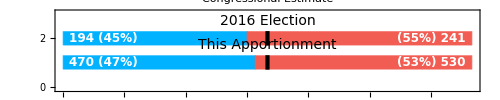

```mathematica
ChartElectionCongress[bigElectionCongress2016]
```